```mathematica
(*ML Data*)

(*differences Y Vector*)
Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\DOCaccuracy.xlsx"];
ΔYVec=Data[[1,All,2]];

nΔYVec=Length[ΔYVec]
```

21

```mathematica
(*the whole Y Vec*)
YVec=Data[[1,All,1]];
n=Length[YVec]
```

21

```mathematica
(*fitting to 90% of the data*)
n90=Floor[nΔYVec (0.9)]
```

18

```mathematica
(*Covariates*)

(*Accuracy Energy*)
X1Vec=Data[[1,All,3]];
(*X3Vec=X3Vec^2;*)

(*Accuracy COOL*)
X2Vec=Data[[1,All,4]];

(*Energy Unknowns*)
X3Vec=Data[[1,All,5]];

(*COOL Unknowns*)
X4Vec=Data[[1,All,6]];
```

```mathematica
(*Plot Y - Observed data*)
```

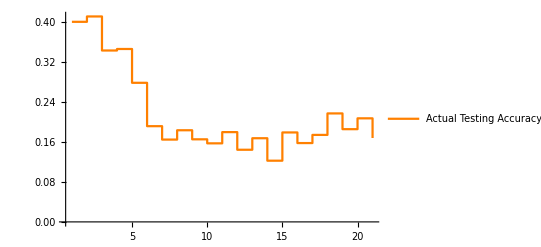

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->0, Joined->True,PlotRange->All,PlotStyle->Orange,PlotLegends->{"Actual Testing Accuracy"}]
```

```mathematica
(* MLR*)
```

```mathematica
(*Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=3)^n90 ((ΔYVec[[i]]-(β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β12 X2[[i]] X3[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]] +β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]))/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];



Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];



Dβ12=Simplify[D[LnL,β12]];





Dβ21=Simplify[D[LnL,β21]];
Dβ22=Simplify[D[LnL,β22]];
Dβ23=Simplify[D[LnL,β23]];
Dβ24=Simplify[D[LnL,β24]];



Dβ28=Simplify[D[LnL,β28]];
Dβ29=Simplify[D[LnL,β29]];
Dβ30=Simplify[D[LnL,β30]];
Dβ31=Simplify[D[LnL,β31]];



Dσ=Simplify[D[LnL,σ]];

RulesInt=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ7},{0==Dβ8},{0==Dβ12},{0==Dβ21},{0==Dβ22},{0==Dβ23},{0==Dβ24},{0==Dβ28},{0==Dβ29},{0==Dβ30},{0==Dβ31},{0==Dσ}},{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β7,0.1},{β8,0.1},{β12,0.1},{β21,0.1},{β22,0.1},{β23,0.1},{β24,0.1},{β28,0.1},{β29,0.1},{β30,0.1},{β31,0.1},{σ,0.1}, MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦3⟧ is longer than depth of object.

Part::partd: Part specification X2⟦3⟧ is longer than depth of object.

Part::partd: Part specification X3⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{β0→-0.224025,β1→0.795103,β2→0.943996,β3→0.0565466,β7→-1.14771,β8→0.0611123,β12→-0.124324,β21→-0.64873,β22→0.163879,β23→-0.0721421,β24→-0.0287458,β28→-0.0508022,β29→-0.153591,β30→0.0608173,β31→-0.00140071,σ→7.18976×10^102}

```mathematica
(*Prediction*)
LRInt=β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β12 X2[[i]] X3[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]] +β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec};
LRInt=LRInt/.RulesInt; 

YFitListInt=.
YFitListInt={ΔYVec[[1]],ΔYVec[[2]]};
For[k=3,k<=nΔYVec,
AppendTo[YFitListInt,LRInt/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec,i->k}]//Quiet;
k=k+1;
];
YFitListInt
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{,0.0107143,-0.0682529,0.00286797,-0.0674573,-0.0860602,-0.026695,0.0210912,-0.0193702,-0.00688628,0.0191524,-0.0326518,0.0170062,-0.0455241,0.0614481,-0.0196395,0.0152847,0.04184,-0.099016,-0.0525286,-0.119061}

```mathematica
YFitCumulativeInt=.
YFitCumulativeInt={YVec[[1]]+YFitListInt[[1]]};
For[k=1,k<(nΔYVec),
AppendTo[YFitCumulativeInt,(YFitCumulativeInt[[k]]+YFitListInt[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulativeInt
```

{0.4+,0.410714+,0.342461+,0.345329+,0.277872+,0.191812+,0.165117+,0.186208+,0.166838+,0.159952+,0.179104+,0.146452+,0.163458+,0.117934+,0.179382+,0.159743+,0.175027+,0.216867+,0.117851+,0.0653229+,-0.0537378+}

```mathematica
YFitCumulativeInt={0.4,0.410714285714286,0.3424613650719731,0.3453293311879583,0.27787199182868894,0.19181183681925923,0.1651168567453649,0.1862080630238245,0.1668378961557177,0.1599516116691366,0.1791039698088327,0.146452153256716,0.16345832585585876,0.11793418848955736,0.17938227145266122,0.15974281057856354,0.17502749109896426,0.21686746987951916,0.11785148674916696,0.0653229011131428,-0.05373776863632211}
```

{0.4,0.410714,0.342461,0.345329,0.277872,0.191812,0.165117,0.186208,0.166838,0.159952,0.179104,0.146452,0.163458,0.117934,0.179382,0.159743,0.175027,0.216867,0.117851,0.0653229,-0.0537378}

```mathematica
failureCount = Table[index,{index,1,n}];
NewPlot=Transpose[{failureCount,YFitCumulativeInt}]
```

{{1,0.4},{2,0.410714},{3,0.342461},{4,0.345329},{5,0.277872},{6,0.191812},{7,0.165117},{8,0.186208},{9,0.166838},{10,0.159952},{11,0.179104},{12,0.146452},{13,0.163458},{14,0.117934},{15,0.179382},{16,0.159743},{17,0.175027},{18,0.216867},{19,0.117851},{20,0.0653229},{21,-0.0537378}}

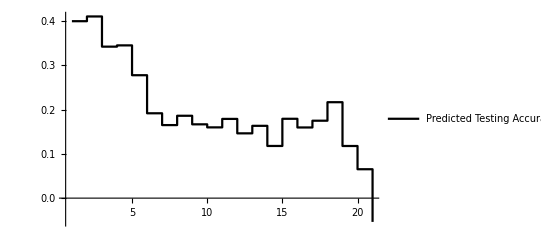

```mathematica
YPredictedPlotInt=ListPlot[(NewPlot),InterpolationOrder->0, Joined->True,PlotStyle->Black,PlotRange->All,PlotLegends->{"Predicted Testing Accuracy"}]
```

Show::gcomb: Could not combine the graphics objects in ….

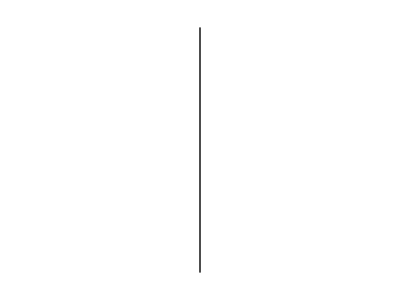
Show[{-Graphics-,-Graphics-},-Graphics-,PlotRange→All]

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)


A=Show[{YObserved,YPredictedPlotInt},Graphics[{Black, Line[{{n90,0},{n90,1}}]}],PlotRange->All]
```

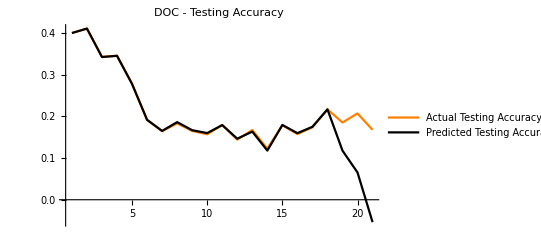

```mathematica
A=ListPlot[{dataPlot,NewPlot},InterpolationOrder->1, Joined->True,PlotStyle->{Orange,Black},PlotRange->All,PlotLegends->{"Actual Testing Accuracy","Predicted Testing Accuracy"},PlotLabel->"DOC - Testing Accuracy"]
```

```mathematica
B=Graphics[{Black, Dashed,Line[{{n90,0},{n90,1}}]}];
```

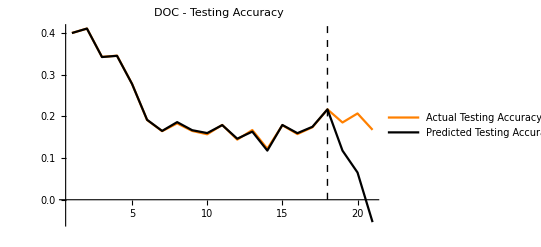

```mathematica
Show[A,B]
```

```mathematica
(*Measure of the quality of the fit (page 60) *)

(*Prediction of Y using X*)
```

```mathematica
(*SSE*)
```

```mathematica
(*SSE=∑_(i=1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.0737641

```mathematica
(*PSSE*)
```

```mathematica
(*PSSE=∑_(i=n90+1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
PSSE=∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.0736976

```mathematica
(*variance*)
```

```mathematica
S2=1/(n-2)(SSE);
```

```mathematica
(*Mean Squared Error*)
MSE=SSE/n;
```

```mathematica
(*Mean Squared Error Predicte data*)
MSEP=PSSE/(n-n90+1)
```

0.0184244

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*values between 0 and 1. The larger the value of r2, the stronger the linear regression between X and Y*)
```

```mathematica
r2=(SSY-SSE)/SSY;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-r2)(n-1)/(n-p-1)/.p->6
```

1-10/7 (1-(-0.0737641+(-0.0867168+1/21 (0.232258-))^2+(-0.0680569+1/21 (0.232258-))^2+(-0.0676041+1/21 (0.232258-))^2+(-0.0449198+1/21 (0.232258-))^2+(-0.0393065+1/21 (0.232258-))^2+(-0.0352564+1/21 (0.232258-))^2+(-0.0315016+1/21 (0.232258-))^2+(-0.0268011+1/21 (0.232258-))^2+(-0.021239+1/21 (0.232258-))^2+(-0.0181118+1/21 (0.232258-))^2+(-0.00804306+1/21 (0.232258-))^2+(0.00302167+1/21 (0.232258-))^2+(0.0107143+1/21 (0.232258-))^2+(0.0163199+1/21 (0.232258-))^2+(0.0186491+1/21 (0.232258-))^2+(0.0216826+1/21 (0.232258-))^2+(0.0224359+1/21 (0.232258-))^2+(0.023042+1/21 (0.232258-))^2+(0.0429544+1/21 (0.232258-))^2+(0.0564792+1/21 (0.232258-))^2+(1/21 (0.232258-)+)^2)/((-0.0867168+1/21 (0.232258-))^2+(-0.0680569+1/21 (0.232258-))^2+(-0.0676041+1/21 (0.232258-))^2+(-0.0449198+1/21 (0.232258-))^2+(-0.0393065+1/21 (0.232258-))^2+(-0.0352564+1/21 (0.232258-))^2+(-0.0315016+1/21 (0.232258-))^2+(-0.0268011+1/21 (0.232258-))^2+(-0.021239+1/21 (0.232258-))^2+(-0.0181118+1/21 (0.232258-))^2+(-0.00804306+1/21 (0.232258-))^2+(0.00302167+1/21 (0.232258-))^2+(0.0107143+1/21 (0.232258-))^2+(0.0163199+1/21 (0.232258-))^2+(0.0186491+1/21 (0.232258-))^2+(0.0216826+1/21 (0.232258-))^2+(0.0224359+1/21 (0.232258-))^2+(0.023042+1/21 (0.232258-))^2+(0.0429544+1/21 (0.232258-))^2+(0.0564792+1/21 (0.232258-))^2+(1/21 (0.232258-)+)^2))